Лабораторная работа 3
Гаврилюк Рената
По-3

```mathematica
Упражнение 10.1а
Row[{Plot[E^x,{x,1,5},ImageSize->500],
	LogLogPlot[E^x,{x,1,5},ImageSize->500]},Spacer[5]] (*row разделяет в данном случае 2 графика 5 пустыми местами*)
```

10.1 а Упражнение

-Graphics--Graphics-

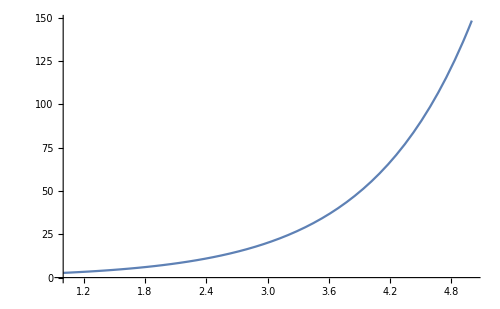

```mathematica
gr1 = Plot[E^x,{x,1,5},ImageSize->500] (*plot - график аналитически заданной функции*)
```

```mathematica
gr2 = LogLogPlot[E^x,{x,1,5},ImageSize->500,  PlotStyle->{Thickness[0.01],Dashing[{0.01,0.04}], Green}] (*logLogPlot-график аналитически заданной фнукции от мин к макс значению в лог-лог шкале - логарифмический по обеим осям*)
```

-Graphics-

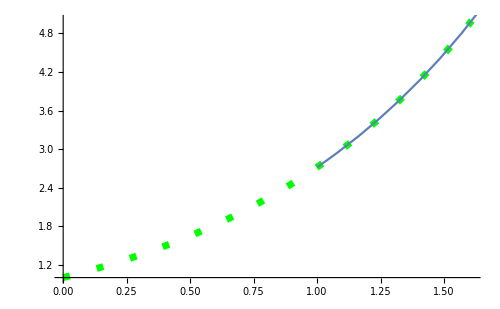

```mathematica
Show[gr2, gr1]
```

```mathematica
Упражнение 10.1b . Генерирует график кривой радиуса Р в зависимости от угла О
fPlt1={4/(2+Cos[t]),4*Cos[t]-2};
g1=Plot[fPlt1,{t,0,2*Pi},ImageSize->500];
g2=PolarPlot[fPlt1,{t,0,2*Pi},ImageSize->500,  PlotStyle->{ Red}]; (*график кривой радиуса fplt1 в зависимости от угла в {} в полярной системем координат*)
Row[{g1,g2},Spacer[15]]
```

10.1 О Р в от угла график кривой радиуса Упражнение зависимости b.Генерирует

-Graphics--Graphics-

```mathematica
Упражнение 10.1c
Row[{PolarPlot[Θ,{Θ,0,4*Pi},ImageSize->500], 
ParametricPlot[{Θ*Cos[Θ],Θ*Sin[Θ]},{Θ,0,4*Pi},ImageSize->500]},Spacer[15]] (*З=ParametricPlot - график кривой заданной параметрически*)
```

10.1 Упражнение c

-Graphics--Graphics-

```mathematica
Упражнение 10.2a . Генерирует график плотности распределени я в процентах по наботу Хi
f3[x_]:=(-E^(-0.2*x^2))*Cos[5*x^2]-0.1*x
list3=Table[f3[x],{x,-5,5,0.4}];
grListLPl=ListLinePlot[list3,BaseStyle->16,
	GridLines->{{5,10,20,25},{-1,-0.5,0.5}},
	Mesh -> Full,Joined->True,
	AxesStyle->Directive[Black,Thick,14],
	Filling->Axis,FillingStyle->LightRed,
	AspectRatio->0.8,ImageSize->500]; (** listLinePlot - линейный график по точкам списка данных*)
grListPSP=ProbabilityScalePlot[list3,BaseStyle->16,
	Mesh -> Full,Joined->True,PlotStyle->Red,
	AxesStyle->Directive[Black,Thick,14],
	Filling->Axis,FillingStyle->LightCyan,
	AspectRatio->0.8,ImageSize->500];(*probabilityScalePlot- график плоности распределения в процентах*)
Row[{grListLPl,grListPSP},Spacer[20]]
```

10.2 в я по график наботу плотности процентах Упражнение распределени Хi a.Генерирует

-Graphics--Graphics-

```mathematica
Упражнение 10.2b
f3[x_]:=(-E^(-0.2*x^2))*Cos[5*x^2]-0.1*x
list3=Table[f3[x],{x,-5,5,0.4}];
grListLPl=ListLinePlot[list3,
	BaseStyle->16,Mesh -> Full,Joined->True,
	AxesStyle->Directive[Black,Thick,14],
	Filling->Axis,FillingStyle->LightRed,
	AspectRatio->0.8,ImageSize->500];
grListQP=QuantilePlot[list3,BaseStyle->16,
	Mesh -> Full,Joined->True,PlotStyle->Green,
	AxesStyle->Directive[Black,Thick,14],
	Filling->Axis,FillingStyle->LightCyan,
	AspectRatio->0.8,ImageSize->500]; (*QuantilePlot - Квантильный q-q график для сравнения совокупности данных с согласованными нормамальным распрделением*)
Row[{grListLPl,grListQP},Spacer[20]]
```

10.2 Упражнение b

-Graphics--Graphics-

```mathematica
Упражнение 10.2c
f3[x_]:=(-E^(-0.2*x^2))*Cos[5*x^2]-0.1*x
list3=Table[f3[x],{x,-5,5,0.4}];
grListLPl=ListLinePlot[list3,
	BaseStyle->16,Mesh -> Full,Joined->True,
	AxesStyle->Directive[Black,Thick,14],
	GridLines->{{5,10,20,25},{-1,-0.5,0.5}},
	GridLinesStyle->Directive[Gray,Dashed],
	
	Filling->Axis,FillingStyle->LightRed,
	AspectRatio->1.,ImageSize->500];

grListPP=ProbabilityPlot[list3,
	BaseStyle->16,Mesh -> Full,Joined->True,
	PlotStyle->Magenta,
	AxesStyle->Directive[Black,Thick,14],
	Filling->Axis,FillingStyle->LightCyan,
	AspectRatio->1.,ImageSize->500];
Row[{grListLPl,grListPP},Spacer[20]]
```

10.2 Упражнение c

-Graphics--Graphics-

```mathematica
Упражнение 10.1d
lstCh1={2,4,8,4};
lstCh2={{2,4},{4,3},{8,2},{4,3}};
grCh1=PieChart[lstCh1,BaseStyle->16,ImageSize->500,
	ChartStyle->{Red,Magenta,Green,Blue},
	ChartLabels->Placed[lstCh1,"RadialOuter"]]; (*PieChart - круговая диаграмма*)

grCh2 = SectorChart[lstCh2,BaseStyle->16,ImageSize->500,
	ChartStyle->{Red,Magenta,Green,Blue},
	ChartLabels->Placed[lstCh2,"RadialOuter"]]; (*SectorChart - секртоная диаграмма*)
Row[{grCh1,grCh2}]
```

10.1 Упражнение d

-Graphics--Graphics-

```mathematica
Упражнение 10.1e . Ступенчатый график от календарного времени
fData0={{{2016,11,17},63},
	{{2016,11,18},64.4},{{2016,11,21},65.0},
	{{2016,11,22},66.3},{{2016,11,23},65.9},
	{{2016,11,25},67.6},{{2016,11,28},66.6},
	{{2016,11,29},67.1},{{2016,11,30},67.5}};

grDLP=DateListPlot[fData0,BaseStyle->14,ImageSize->500]; (*DateListPlot -  график от календарного времени*)
grDLSP=DateListStepPlot[fData0,BaseStyle->14,ImageSize->500];(*DateListStepPlot - ступенчатый график от календарного времени*)

Row[{grDLP,grDLSP},Spacer[20]]
```

10.1 от график времени Упражнение календарного e.Ступенчатый

-Graphics--Graphics-

```mathematica
Упражнение 10.1f
fdataOHLCV={{{2017,10,23},{65.9,68.,64.9,67.5,53950}},
{{2017,10,24},{67.6,67.8,66.3,66.9,31740}},
{{2017,10,25},{66.6,67.6,66.1,66.9,48200}},
{{2017,10,26},{67.1,68.1,66.5,67.5,66750}},
{{2017,10,27},{67.5,67.9,65.8,65.9,38080}}};

grTrCh=TradingChart[fdataOHLCV,AspectRatio->7/10,
	ImageSize->260,TrendStyle->{Blue,Magenta}]; (*TradingChart - торговый график, показывает цены и объемы продаж на каждую дату диапазона*)
grITrCh=InteractiveTradingChart[fdataOHLCV,AspectRatio->7/10,ImageSize->220];
Row[{grTrCh,grITrCh},Spacer[10]]
```

10.1 Упражнение f

InteractiveTradingChart::cloudf: InteractiveTradingChart is not currently supported in the Wolfram Cloud.

-Graphics-$Failed

```mathematica
Упражнение 10.1g. Линии тока на плоскости 
grfCP1=ContourPlot[{Cos[x+y^2]*2y Cos[x+y^2]},{x,-2,2},
{y,-2,2},ColorFunction->"DeepSeaColors", Contours->10,BaseStyle->{12},ImageSize->500]; (*ContourPlot- контурный график на плосковсти, показывает линии равного уровня*)
grStrPl1=
	StreamPlot[{Cos[x+y^2],2y Cos[x+y^2]},{x,-2,2},{y,-2,2},
	StreamStyle->Blue,BaseStyle->{12},ImageSize->500]; (*StreamPlot - линии тока на плоскости - диаграмма потоков*)
Row[{grfCP1,grStrPl1},Spacer[10]]
```

10.1 на тока плоскости Упражнение g.Линии

-Graphics--Graphics-

10.1 в с по виде графы дерева разными глубинам уровнями выражений Упражнение деревовидные h.Изображение

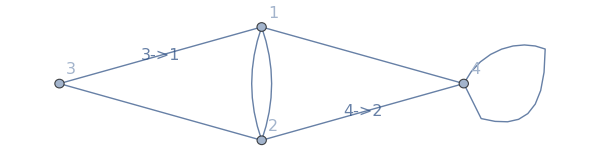

-Graphics-

```mathematica
Упражнение 10.1h . Изображение выражений в виде дерева с разными уровнями по глубинам(деревовидные графы)
fTrFrm={1->2,2->1,{3->1,"3->1"},
	3->2,4->1,{4->2,"4->2"},4->4};

GraphPlot[fTrFrm,VertexLabeling->True,
	BaseStyle->16,AspectRatio->3/10,ImageSize->600] (*GraphPlot - визуализация графа*)

TreeForm[fTrFrm,DirectedEdges->True,BaseStyle->16,
	VertexLabeling->True,AspectRatio->3/10,
ImageSize->600] (*TreePlot - графическое дерево графа на плоскости*)
```